```mathematica
l=48;
ll=ToString[l];
d=0.221654;
dd=ToString[d];
histd[d][l]={};
data[l]={};
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EMHL-l"<>ll<>"-k"<>dd<>"-run"<>ii<>".txt",{Number,Number,Number,Number,Number,Number}];
data[l]=Join[data[l],data[i][l]];
,{i,{1}}
]
data[l]=Sort[data[l],#1[[1]]<#2[[1]]&];

his[l]=Table[{data[l][[All,1]][[i]],data[l][[All,2]][[i]]},{i,1,Length[data[l]]}];
```

```mathematica
Do[

nor[l]=Sum[his[l][[All,2]][[i]],{i,1,Length[his[l]]}];
his[l]=Table[{his[l][[All,1]][[i]],his[l][[All,2]][[i]]/nor[l]},{i,1,Length[his[l]]}];
,{l,{8,12,16,24,32,48}}]
```

```mathematica
l=24;
his[l]=Table[{data[1][l][[All,1]][[i]],data[1][l][[All,2]][[i]]},{i,1,Length[data[1][l]]}];
```

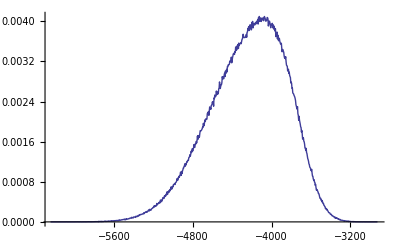

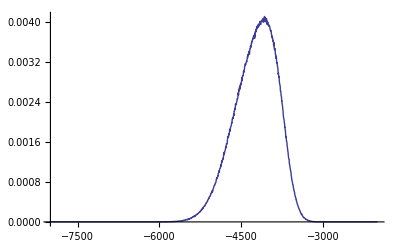

```mathematica
ListLinePlot[{his[16]}]
ListLinePlot[{pdf[k0][16]}]
```

```mathematica
Length[his[32]]
Length[Sort[his[32],#1[[1]]<#2[[2]]&]]
```

8562

8562

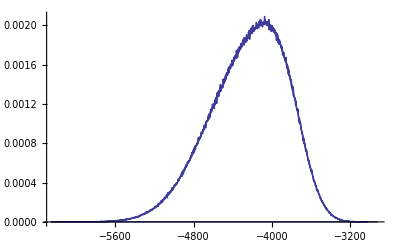

```mathematica
ListLinePlot[his[16]]
```

```mathematica
l=16;
k0=0.221654;
k=0.21;
z[k][l]=Sum[his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]],{i,1,Length[his[l]]}]
hist[k][l]=Table[{his[l][[All,1]][[i]],his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]]/z[k][l]},{i,1,Length[his[l]]}];
```

1.20229×10^-19

```mathematica
Sum[hist[0.22][16][[All,2]][[i]],{i,1,Length[hist[0.224][16]]}]
```

1.

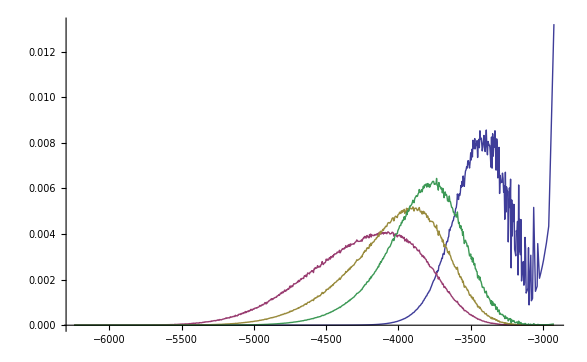

```mathematica
ListLinePlot[{hist[0.21][l],his[l],hist[0.22][l],hist[0.218][l]},PlotRange->Full]
```

```mathematica
ClearAll[m,absm,m2,m4]
```

```mathematica
k0=0.221654;

Do[
m[l]={};
absm[l]={};
m2[l]={};
m4[l]={};
u[l]={};


For[k=0.22075,k<0.22225,k += 0.00005,
z[k][l]=Sum[his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]],{i,1,Length[his[l]]}];
hist[k][l]=Table[{his[l][[All,1]][[i]],his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]]/z[k][l]},{i,1,Length[his[l]]}];
m[l]=Append[m[l],{k,Sum[hist[k][l][[All,2]][[i]]*data[l][[All,3]][[i]],{i,1,Length[hist[k][l]]}]}];
absm[l]=Append[absm[l],{k,Sum[hist[k][l][[All,2]][[i]]*data[l][[All,4]][[i]],{i,1,Length[hist[k][l]]}]}];
m2[l]=Append[m2[l],{k,k*l^3*Sum[hist[k][l][[All,2]][[i]]*(data[l][[All,5]][[i]]-data[l][[All,3]][[i]]*data[l][[All,3]][[i]]),{i,1,Length[hist[k][l]]}]}];
m4[l]=Append[m4[l],{k,Sum[hist[k][l][[All,2]][[i]]*data[l][[All,6]][[i]],{i,1,Length[hist[k][l]]}]}];
u[l]=Append[u[l],{k,Sum[hist[k][l][[All,2]][[i]]*(1-data[l][[All,6]][[i]]/(3*data[l][[All,5]][[i]])),{i,1,Length[hist[k][l]]}]}]
]
,{l,{8,12,16,24,32,48}}]
```

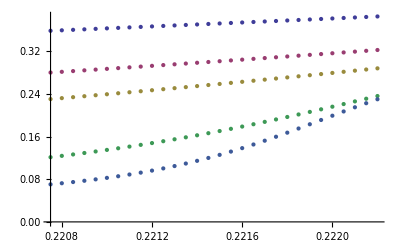

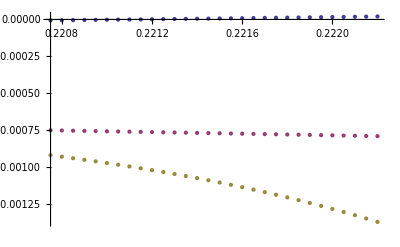

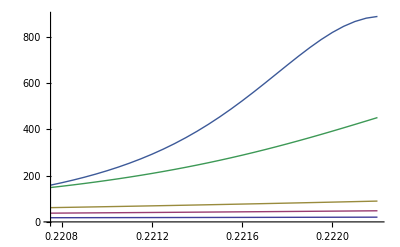

```mathematica
ListPlot[{absm[8],absm[12],absm[16],absm[32],absm[48]}]
ListPlot[{m[8],m[12],m[16]}]
ListLinePlot[{m2[8],m2[12],m2[16],m2[32],m2[48]}]
```

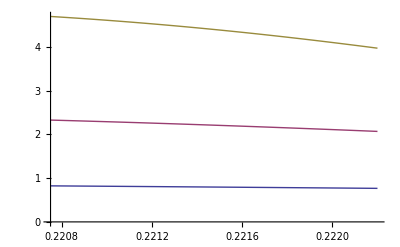

```mathematica
ListLinePlot[{m2[8],m2[12],m2[16]}]
```

```mathematica
Do[
dm2dk[l]=Table[{m2[l][[All,1]][[i]],((m2[l][[All,2]][[i+1]]-m2[l][[All,2]][[i]])/(m2[l][[All,1]][[i+1]]-m2[l][[All,1]][[i]]))/m2[l][[All,2]][[i]]},{i,1,Length[u[l]]-1}];
,{l,{8,12,16,24,32,48}}]
```

```mathematica
Do[
dudk[l]=Table[{u[l][[All,1]][[i]],((u[l][[All,2]][[i+1]]-u[l][[All,2]][[i]])/(u[l][[All,1]][[i+1]]-u[l][[All,1]][[i]]))/u[l][[All,2]][[i]]},{i,1,Length[u[l]]-1}];
,{l,{8,12,16,24,32,48}}]
```

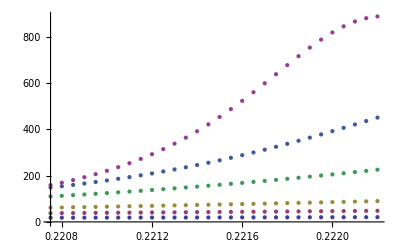

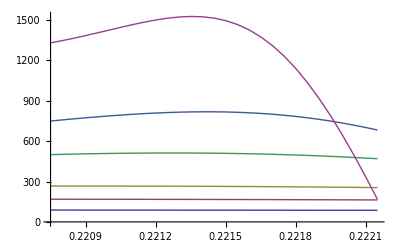

```mathematica
ListPlot[{m2[8],m2[12],m2[16],m2[24],m2[32],m2[48]}]
ListLinePlot[{dm2dk[8],dm2dk[12],dm2dk[16],dm2dk[24],dm2dk[32],dm2dk[48]}]
```

```mathematica
sdln=Table[{l,Max[dm2dk[l][[All,2]]]},{l,{8,12,16,24,32,48}}]
```

{{8,88.0032},{12,168.429},{16,266.12},{24,511.855},{32,817.832},{48,1526.14}}

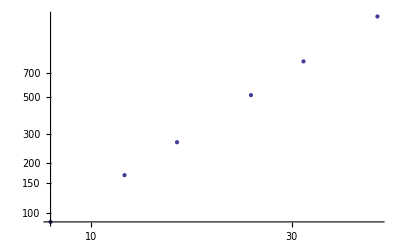

```mathematica
ListLogLogPlot[sdln]
```

```mathematica
(7.330494987039905-4.477373221064632)/(Log[48]-Log[8])
```

1.59236

```mathematica
k0=0.221654;

Do[
m[l]={};
absm[l]={};
m2[l]={};
m4[l]={};
u[l]={};


For[k=0.221654,k<0.22225,k += 0.05,
z[k][l]=Sum[his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]],{i,1,Length[his[l]]}];
hist[k][l]=Table[{his[l][[All,1]][[i]],his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]]/z[k][l]},{i,1,Length[his[l]]}];
m[l]=Append[m[l],{k,Sum[hist[k][l][[All,2]][[i]]*data[l][[All,3]][[i]],{i,1,Length[hist[k][l]]}]}];
absm[l]=Append[absm[l],{k,Sum[hist[k][l][[All,2]][[i]]*data[l][[All,4]][[i]],{i,1,Length[hist[k][l]]}]}];
m2[l]=Append[m2[l],{k,k*l^3*Sum[hist[k][l][[All,2]][[i]]*(data[l][[All,5]][[i]]-data[l][[All,3]][[i]]*data[l][[All,4]][[i]]),{i,1,Length[hist[k][l]]}]}];
m4[l]=Append[m4[l],{k,Sum[hist[k][l][[All,2]][[i]]*data[l][[All,6]][[i]],{i,1,Length[hist[k][l]]}]}];
u[l]=Append[u[l],{k,Sum[hist[k][l][[All,2]][[i]]*(1-data[l][[All,6]][[i]]/(3*data[l][[All,5]][[i]])),{i,1,Length[hist[k][l]]}]}]
]
,{l,{8,12,16,24,32,48}}]
```

```mathematica
Sum[his[l][[All,2]][[i]]*data[l][[All,4]][[i]],{i,1,Length[his[l]]}]
```

0.264774

```mathematica
k=0.221654
l=16
Sum[k*l^3*his[l][[All,2]][[i]]*(data[l][[All,5]][[i]]-data[l][[All,3]][[i]]*data[l][[All,3]][[i]]),{i,1,Length[his[l]]}]
```

0.221654

16

78.1533

```mathematica
his[l][[5]]
data[l][[5]]
```

{-6104,1/2000000}

{-6104,1,-0.610352,0.610352,0.372529,0.138778}

```mathematica
{0.2216,0.0268756}
{0.2216,78.33495662927963}
```

```mathematica
χ2[16]
```

{{0.215,18.6013},{0.2152,17.1822},{0.2154,17.5959},{0.2156,18.68},{0.2158,19.9641},{0.216,19.4093},{0.2162,20.2437},{0.2164,22.505},{0.2166,23.1174},{0.2168,24.8027},{0.217,24.0962},{0.2172,25.0768},{0.2174,26.476},{0.2176,28.2216},{0.2178,29.7301},{0.218,30.4216},{0.2182,31.2447},{0.2184,33.7949},{0.2186,36.4654},{0.2188,38.7169},{0.219,41.6856},{0.2192,40.062},{0.2194,43.4651},{0.2196,47.2974},{0.2198,50.0489},{0.22,50.6694},{0.2202,52.5119},{0.2204,55.6003},{0.2206,56.76},{0.2208,59.4991},{0.221,67.5854},{0.2212,67.8585},{0.2214,72.9463},{0.2216,78.335},{0.2218,76.5084},{0.222,81.7991},{0.2222,88.1421},{0.2224,99.5181},{0.2226,98.1702},{0.2228,104.368},{0.223,107.009},{0.2232,112.262},{0.2234,117.302},{0.2236,128.334},{0.2238,128.1},{0.224,124.731},{0.2242,139.385},{0.2244,141.052},{0.2246,135.58},{0.2248,148.946},{0.225,161.136},{0.2252,169.604},{0.2254,176.758},{0.2256,121.085},{0.2258,184.947},{0.226,110.295},{0.2262,155.937},{0.2264,99.6123},{0.2266,80.7886},{0.2268,164.516},{0.227,140.443},{0.2272,218.754},{0.2274,174.75},{0.2276,157.086},{0.2278,64.2978},{0.228,5.11661},{0.2282,3.90321},{0.2284,173.519},{0.2286,3.93489},{0.2288,3.67893},{0.229,3.18711},{0.2292,3.27909},{0.2294,3.01515},{0.2296,2.9328},{0.2298,2.94335},{0.23,2.66299},{0.2302,2.54184},{0.2304,2.61748},{0.2306,2.46899},{0.2308,2.40903},{0.231,2.48864},{0.2312,2.27679},{0.2314,2.18492},{0.2316,2.07226},{0.2318,2.05352},{0.232,1.99929},{0.2322,1.9853},{0.2324,1.94783},{0.2326,1.96015},{0.2328,1.83634},{0.233,1.8162},{0.2332,1.78436},{0.2334,1.61465},{0.2336,1.66031},{0.2338,1.67834},{0.234,1.59604},{0.2342,1.4843},{0.2344,1.52589},{0.2346,1.46307},{0.2348,1.50913}}

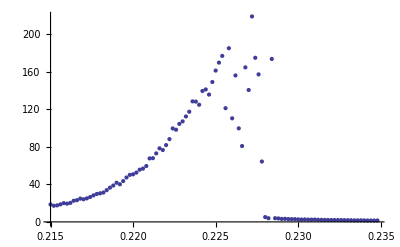

```mathematica
ListPlot[χ2[16]]
```